```mathematica
(*Аналитическое решение*)
DSolve[{y'[x]== 3*Sin[x]-y[x]},y,x]
```

{{y→Function[{x},ⅇ^-x C[1]+3/2 (-Cos[x]+Sin[x])]}}

```mathematica
Sol=DSolve[{y'[x]== x*y[x],y[0] == 1},y,x];
```

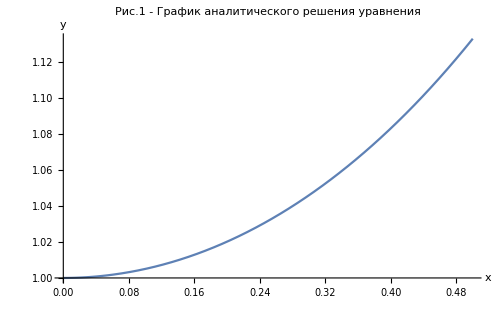

```mathematica
Plot[{y[x]/.Sol},{x,0,0.5},AxesLabel->{"x","y"},PlotLabel->"Рис.1 - График аналитического решения уравнения"]
```

```mathematica
(*Проверка устойчивости*)
dSol=DSolve[{z'[x]-10^-2== 3*Sin[x]-z[x],z[0] == 10^-3},z,x];
```

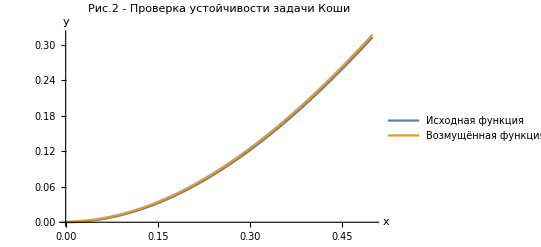

```mathematica
Plot[{y[x]/.Sol,z[x]/.dSol},{x,0,0.5},PlotLegends->{"Исходная функция","Возмущённая функция"},AxesLabel->{"x","y"},PlotLabel->"Рис.2 - Проверка устойчивости задачи Коши"]
```

```mathematica
(*Метод 1 порядка точности*)
Sol1=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution1.txt",{Number,Number}];
```

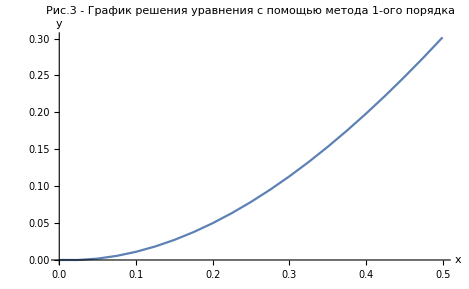

```mathematica
ListLinePlot[{Sol1},AxesLabel->{"x","y"},PlotLabel->"Рис.3 - График решения уравнения с помощью метода 1-ого порядка"]
```

```mathematica
(*Методы 2 порядка точности*)
Sol21=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution2.txt",{Number,Number}];
```

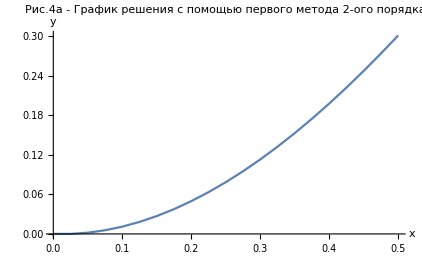

```mathematica
ListLinePlot[{Sol1},PlotLabel->"Рис.4а - График решения с помощью первого метода 2-ого порядка",AxesLabel->{"x","y"}]
```

```mathematica
Sol22=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution2.txt",{Number,Number}];
```

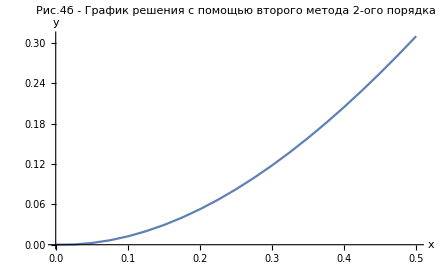

```mathematica
ListLinePlot[{Sol22},PlotLabel->"Рис.4б - График решения с помощью второго метода 2-ого порядка",AxesLabel->{"x","y"}]
```

```mathematica
Sol23=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution2.txt",{Number,Number}];
```

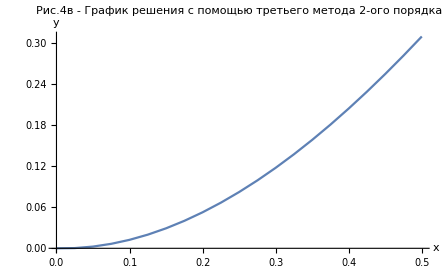

```mathematica
ListLinePlot[{Sol23},PlotLabel->"Рис.4в - График решения с помощью третьего метода 2-ого порядка",AxesLabel->{"x","y"}]
```

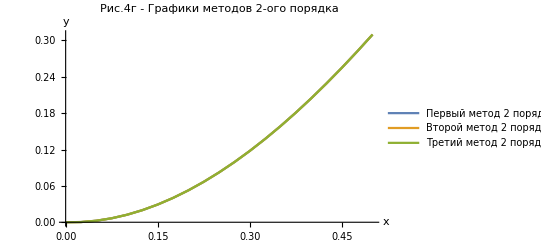

```mathematica
ListLinePlot[{Sol21,Sol22,Sol23},PlotLegends->{"Первый метод 2 порядка","Второй метод 2 порядка","Третий метод 2 порядка"},AxesLabel->{"x","y"},PlotLabel->"Рис.4г - Графики методов 2-ого порядка"]
```

```mathematica
(*Методы 3 порядка точности*)
```

```mathematica
Sol31=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution3.txt",{Number,Number}];
```

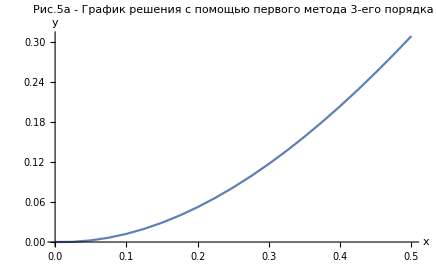

```mathematica
ListLinePlot[{Sol31},PlotLabel->"Рис.5а - График решения с помощью первого метода 3-его порядка",AxesLabel->{"x","y"}]
```

```mathematica
Sol32=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution3.txt",{Number,Number}];
```

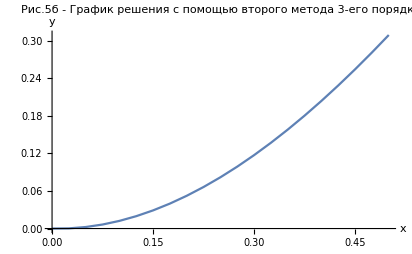

```mathematica
ListLinePlot[{Sol32},PlotLabel->"Рис.5б - График решения с помощью второго метода 3-его порядка",AxesLabel->{"x","y"}]
```

```mathematica
Sol33=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution3.txt",{Number,Number}];
```

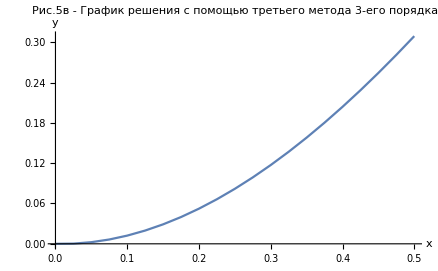

```mathematica
ListLinePlot[{Sol33},PlotLabel->"Рис.5в - График решения с помощью третьего метода 3-его порядка",AxesLabel->{"x","y"}]
```

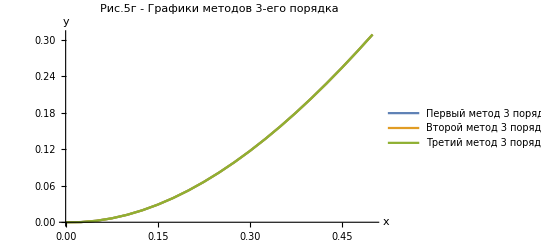

```mathematica
ListLinePlot[{Sol31,Sol32,Sol33},PlotLegends->{"Первый метод 3 порядка","Второй метод 3 порядка","Третий метод 3 порядка"},AxesLabel->{"x","y"},PlotLabel->"Рис.5г - Графики методов 3-его порядка"]
```

```mathematica
(*Методы 4 порядка точности*)
Sol41=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution4.txt",{Number,Number}];
```

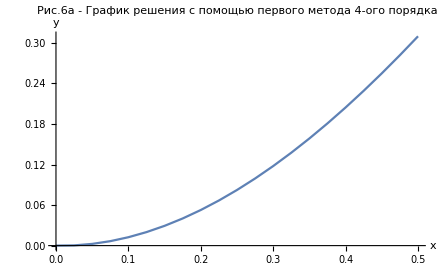

```mathematica
ListLinePlot[{Sol41},PlotLabel->"Рис.6а - График решения с помощью первого метода 4-ого порядка",AxesLabel->{"x","y"}]
```

```mathematica
Sol42=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution4.txt",{Number,Number}] ;
```

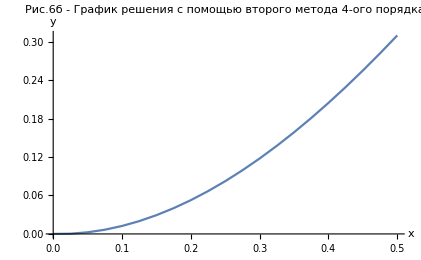

```mathematica
ListLinePlot[{Sol42},PlotLabel->"Рис.6б - График решения с помощью второго метода 4-ого порядка",AxesLabel->{"x","y"}]
```

```mathematica
Sol43=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\Solution4.txt",{Number,Number}];
```

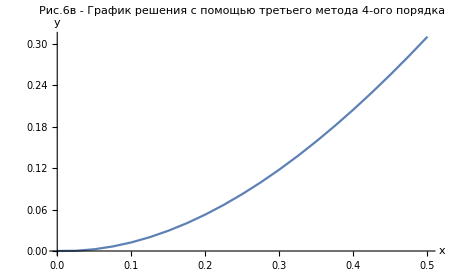

```mathematica
ListLinePlot[{Sol43},PlotLabel->"Рис.6в - График решения с помощью третьего метода 4-ого порядка",AxesLabel->{"x","y"}]
```

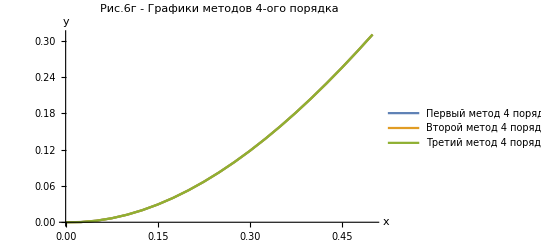

```mathematica
ListLinePlot[{Sol41,Sol42,Sol43},PlotLegends->{"Первый метод 4 порядка","Второй метод 4 порядка","Третий метод 4 порядка"},AxesLabel->{"x","y"},PlotLabel->"Рис.6г - Графики методов 4-ого порядка"]
```

```mathematica
(*Сравниваем с аналитическим решением*)
Y=Table[0,{i,21},{j,2}];
For[i=1,i≤21,i++,
Y[[i,2]]=y[i-(0.975*i+0.025)]/.Sol[[1]];
Y[[i,1]] =i-(0.975*i+0.025);
]
```

```mathematica
Sol2 = Sol21;
Sol3=Sol31;
Sol4=Sol41;
```

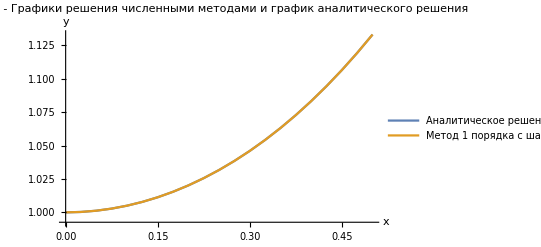

```mathematica
ListLinePlot[{Y,Sol4},PlotLegends->{"Аналитическое решение","Метод 1 порядка c шагом 0.025","Метод 2 порядка c шагом 0.025","Метод 3 порядка c шагом 0.025","Метод 4 порядка c шагом 0.025"},AxesLabel->{"x","y"},PlotLabel->"Рис.7 - Графики решения численными методами и график аналитического решения"]
```

```mathematica
(*Проверяем сходимость*)
SolPres1=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\SolutionPres1.txt",{Number,Number}]
SolPres2=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\SolutionPres2.txt",{Number,Number}]
SolPres3=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\SolutionPres3.txt",{Number,Number}]
SolPres4=ReadList["C:\\Users\\Коптутер\\source\\repos\\4RK(1)\\4RK(1)\\SolutionPres4.txt",{Number,Number}]
(*eps1=Table[0,{i,12},{j,2}];
For[i=1,i≤12,i++,
eps1[[i,1]]=Y[[i,1]];
eps1[[i,2]]=Y[[i,2]]-Sol1[[i,2]];
]
eps2=Table[0,{i,12},{j,2}];
For[i=1,i≤12,i++,
eps2[[i,1]]=Y[[i,1]];
eps2[[i,2]]=Y[[i,2]]-Sol2[[i,2]];
]
eps3=Table[0,{i,12},{j,2}];
For[i=1,i≤12,i++,
eps3[[i,1]]=Y[[i,1]];
eps3[[i,2]]=Y[[i,2]]-Sol3[[i,2]];
]
eps4=Table[0,{i,12},{j,2}];
For[i=1,i≤12,i++,
eps4[[i,1]]=Y[[i,1]];
eps4[[i,2]]=Y[[i,2]]-Sol4[[i,2]];
]*)
```

{{0.1,1.01809},{0.05,0.0686552},{0.025,0.059055}}

{{0.1,0.377711},{0.05,0.0315052},{0.025,0.0167398}}

{{0.1,0.161541},{0.05,0.0129273},{0.025,0.0074804}}

{{0.1,0.0755432},{0.05,0.00630746},{0.025,0.0033241}}

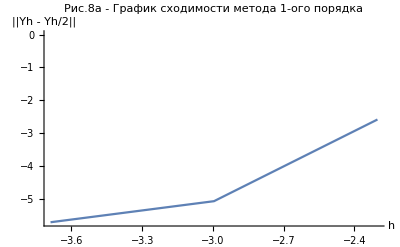

```mathematica
ListLinePlot[{Log[SolPres4]},PlotLabel->"Рис.8а - График сходимости метода 1-ого порядка",AxesLabel->{"h","||Yh - Yh/2||"}]
```

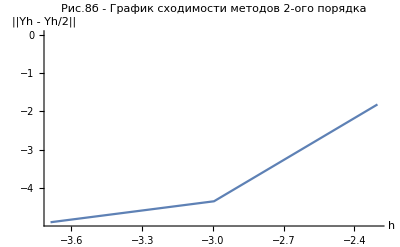

```mathematica
ListLinePlot[{Log[SolPres3]},PlotLabel->"Рис.8б - График сходимости методов 2-ого порядка",AxesLabel->{"h","||Yh - Yh/2||"}]
```

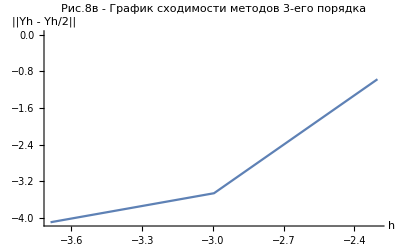

```mathematica
ListLinePlot[{Log[SolPres2]},PlotLabel->"Рис.8в - График сходимости методов 3-его порядка",AxesLabel->{"h","||Yh - Yh/2||"}]
```

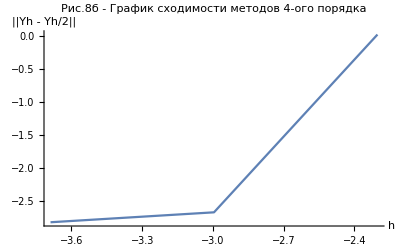

```mathematica
ListLinePlot[{Log[SolPres1]},PlotLabel->"Рис.8б - График сходимости методов 4-ого порядка",AxesLabel->{"h","||Yh - Yh/2||"}]
```

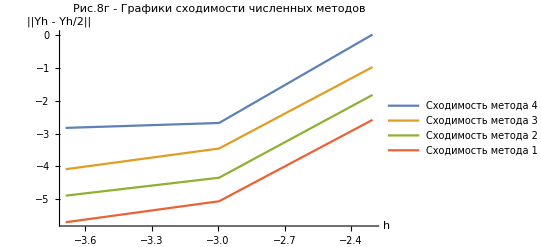

```mathematica
ListLinePlot[{Log[SolPres1],Log[SolPres2],Log[SolPres3],Log[SolPres4]},PlotLegends->{"Cходимость метода 4 порядка","Cходимость метода 3 порядка","Cходимость метода 2 порядка","Cходимость метода 1 порядка"},AxesLabel->{"h","||Yh - Yh/2||"},PlotLabel->"Рис.8г - Графики сходимости численных методов"]
```